Last modified on: Sunday, July 15, 2018 at 14:39

Author Info

Madeleine Sutherland

Paul Abbott

Massachusetts Institute of Technology
Collaborator: Robert Nachbar

Poster Session Content

Interpreting Drug Quantitative Structure-Activity Relationship (QSAR) Data in Mathematica

Investigate the applicability of WL machine learning and other functionality to the analysis of drug QSAR data. Build models that can be applied to experimental design in the real world.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

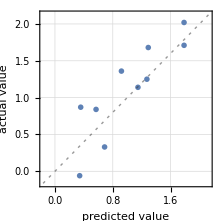
Wolfram Language facilitates data analysis and 3D structure image generation. 
However, for this data set, machine learning models provide no advantage over 
Multiple Non-Linear Regression.
-Graphics-         -Graphics-
Left: Actual vs Predicted logMU’s (log of ratio of effective dose for test compound vs the reference mescaline) from Aouidate, et al’s Multiple Non-Linear Regression.1 
Right: Actual vs Predicted logMU’s from Predict[]. Noting the difference in scale, the two are comparable.

• Generate more chemically diverse data sets, try feeding them into a neural net 
• Map calculated electron density data over 3D chemical structure grid
• Test ability of neural net to predict target engagement of drug structures from rich, structurally diverse SAR data.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Background: So What is QSAR Anyway?

Stages of Drug Development:

QSAR and the Wolfram Language

• WL was efficient for Principal Component Analysis, correlation matrix generation, 
normalization, and multiple linear and nonlinear regression
• I developed a flexible function for “backwards” regression/comparison of models, 
with help from Kyle Keane
• Robert Nachbar and I created 3D image generation functions that will help compare
electronic structures in the future
• It’s possible neural nets will help to generate models from some data sets

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

## Introduction and Background

#### Understanding and optimizing drug activity through QSAR

In drug development, initial screening of thousands or millions of compounds yields a handful of compounsd with the biological activity sought.  The medicinal value of hit molecules is then optimized via Quantitative Structure-Activity Relationships, or QSAR.  QSAR seeks to explain the variation in the biological activity of related molecules via variations in their structure and physicochemical properties.  When the drug’s binding partner in the cell is known, we are optimizing that binding constant.  Otherwise, we optimize the biological outcome at a gross level via measurements like effective dose.  Synthesizing and testing new compounds is time-consuming and expensive, so the faster we can reach a mathematical model with predictive power, the better.

#### Electronic Descriptors and Density Functional Theory

The physicochemical properties of compounds used in such studies are ultimately a function of the compounds’ electronic structure.  The electronic structure of molecules can be estimated using Density Functional Theory, or DFT.  This is a computationally intensive process, but newer software is becoming more efficient and accessible.   Recently there has been increasing interest in the applicability of electronic descriptors from DFT to QSAR studies.

#### Introduction to the Publication Under Study:

Aouidate, et al collected from the literature the biochemical activities of 46 phenalkylamines, a frequently-abused class of psychoactive drugs.  For phenylalkylamines, the mechanism of action is poorly understood so activity is expressed as logMU, the log of the effective doses of the compound under study to mescaline (higher log ratios indicate greater activity).  The authors calculated from DFT the descriptors Etotal, Ehomo and Elumo (energies of the highest occupied and lowest unoccupied molecular orbitals), dipole moment (DM), and absolute hardness (η), and physicochemical properties such as molecular weight, density, and octanol/water partition coefficient (logP).  They then used Principal Component Analysis to estimate the number of variables needed to explain the variance in data, and did “backwards” linear and nonlinear regression to build a mathematical model for activity.  By comparing many possible models, they found that the best models made heavy use of the DFT descriptors.

## Results and Discussion

## Initial Data Analysis:

### Goals:

This part of the project began in January at MIT in Professor Kyle Keane’s Mathematica class, but was formalized here.
Goals:
• Replicate data analysis from Aouidate, et al’s publication on the use of DFT descriptors in QSAR studies. 
• Normalize the data and add in more traditional descriptors; test whether that affects the model.

### Code:

Functions to Normalize Data:

I created a package of functions I now use all the time for data normalization:

```mathematica
<<DataImportandNormalization`
```

These functions delete rows and columns of zeros and nulls:

```mathematica
m={{1,2,3,0},{2,6,1,0},{0,0,0,0}}
```

{{1,2,3,0},{2,6,1,0},{0,0,0,0}}

```mathematica
m2=deleteZeroRows[m]
```

{{1,2,3,0},{2,6,1,0}}

```mathematica
m3=deleteZeroColumns[m2]
```

{{1,2,3},{2,6,1}}

Now for our data:

```mathematica
importedData=Import["/Users/themarchhare/Documents/GitHub/Project/Molecular Structures Real/Table of Aouidate data.xlsx"][[1]];
```

```mathematica
data=ReplaceAll[importedData,s_String:>ToExpression[s]];
```

```mathematica
data1=deleteZeroRows[data];
```

```mathematica
data2=deleteZeroColumns[data1];
```

```mathematica
Transpose[data2]
```

(logMU | 2.72 | 1.96 | 2.02 | 1.95 | 1.9 | 1.71 | 1.69 | 1.68 | 1.66 | 1.36 | 1.33 | 1.25 | 1.29 | 1.27 | 1.14 | 1.36 | 1.11 | 1. | 1.05 | 1. | 1.38 | 0.87 | 0.86 | 0.83 | 0.84 | 0.84 | 0.81 | 0.76 | 0.66 | 0.68 | 0.67 | 0.59 | 0.58 | 0.46 | 0.43 | 0.41 | 0.38 | 0.38 | 0.38 | 0.33 | 0.23 | 0.03 | 0. | -0.03 | -0.06 | -0.67
ET | -82328.7 | -30241. | -19406.4 | -20476.1 | -18336.7 | -31310.7 | -86156.7 | -21545.9 | -29171.2 | -29171. | -20382.8 | -18336.6 | -30240.9 | -17266.8 | -22396.4 | -21452.6 | -28101.4 | -19280.5 | -21452.6 | -19280.5 | -22522.4 | -20382.8 | -23498.6 | -21452.5 | -29171. | -29171. | -28101.4 | -22396.4 | -29171. | -30240.9 | -17266.9 | -12104.5 | -31310.5 | -26669.7 | -19280.5 | -16164.5 | -22522.2 | -30240.9 | -30240.9 | -20382.8 | -21452.6 | -20382.7 | -19312.9 | -19312.8 | -17266.8 | -16196.9
IP | 7.374 | 7.125 | 6.731 | 6.724 | 6.765 | 7.238 | 7.374 | 6.721 | 7.121 | 6.993 | 6.83 | 6.802 | 7.156 | 8.353 | 7.075 | 6.803 | 7.292 | 7.265 | 7.265 | 6.803 | 6.911 | 7.265 | 7.374 | 7.183 | 7.129 | 7.102 | 7.319 | 7.02 | 7.047 | 7.02 | 7.047 | 7.809 | 7.02 | 7.238 | 7.211 | 7.211 | 7.156 | 7.02 | 7.156 | 7.319 | 7.129 | 7.238 | 7.319 | 7.456 | 7.292 | 7.292
EHOMO | -5.682 | -5.428 | -5.029 | -5.037 | -5.009 | -4.78 | -5.687 | -5.025 | -5.453 | -5.327 | -5.101 | -5.024 | -5.333 | -5.142 | -5.349 | -5.073 | -5.423 | -5.393 | -5.505 | -4.968 | -5.063 | -5.505 | -5.703 | -5.443 | -5.499 | -5.569 | -5.536 | -5.281 | -5.407 | -5.303 | -5.243 | -5.971 | -5.311 | -5.59 | -5.328 | -5.293 | -5.435 | -5.247 | -5.533 | -5.524 | -5.41 | -5.481 | -5.523 | -5.719 | -5.444 | -5.443
η | 5.522 | 5.258 | 5.302 | 5.295 | 5.282 | 5.066 | 5.527 | 5.3 | 5.295 | 5.234 | 5.576 | 5.301 | 5.236 | 5.451 | 5.755 | 5.531 | 5.335 | 5.876 | 5.911 | 5.226 | 5.528 | 5.908 | 5.961 | 5.831 | 5.468 | 5.499 | 5.488 | 5.594 | 5.332 | 5.221 | 5.765 | 6.34 | 5.224 | 5.669 | 5.872 | 5.602 | 5.827 | 5.533 | 5.466 | 5.912 | 5.794 | 5.872 | 5.914 | 6.007 | 5.849 | 5.848
ELUMO | -0.16 | -0.17 | 0.273 | 0.258 | 0.273 | 0.286 | -0.16 | 0.275 | -0.158 | -0.093 | 0.475 | 0.278 | -0.097 | 0.309 | 0.407 | 0.458 | -0.088 | 0.483 | 0.406 | 0.258 | 0.465 | 0.403 | 0.257 | 0.389 | -0.03 | -0.07 | -0.049 | 0.313 | -0.075 | -0.082 | 0.522 | 0.37 | -0.088 | 0.079 | 0.544 | 0.309 | 0.391 | 0.286 | -0.067 | 0.388 | 0.384 | 0.39 | 0.391 | 0.288 | 0.405 | 0.406
DM | 3.242 | 1.996 | 1.234 | 1.283 | 1.117 | 2.498 | 3.271 | 1.25 | 2.115 | 4.017 | 3.159 | 1.323 | 4.084 | 1.618 | 1.297 | 3.234 | 4.378 | 1.539 | 3.041 | 1.505 | 3.276 | 3.089 | 1.288 | 2.994 | 3.92 | 3.714 | 4.009 | 0.427 | 4.42 | 4.043 | 2.553 | 1.567 | 4.067 | 3.375 | 1.369 | 1.899 | 2.947 | 3.05 | 3.751 | 3.136 | 2.979 | 3.237 | 3.203 | 1.449 | 3.673 | 3.724
Qp | 0.046 | 0.135 | 0.126 | 0.126 | 0.127 | -0.15 | 0.046 | 0.122 | -0.131 | -0.219 | 0.349 | 0.125 | -0.22 | 0.133 | 0.273 | 0.353 | -0.223 | 0.326 | 0.265 | 0.326 | 0.352 | 0.225 | 0.269 | 0.264 | 0.293 | 0.289 | 0.293 | 0.283 | -0.226 | -0.222 | 0.378 | 0.179 | -0.219 | 0.267 | 0.265 | 0.329 | 0.265 | 0.3 | 0.285 | 0.245 | 0.26 | 0.249 | 0.253 | 0.305 | 0.308 | 0.307
Qmin | -0.707 | -0.708 | -0.712 | -0.709 | -0.71 | -0.712 | -0.709 | -0.713 | -0.707 | -0.713 | -0.713 | -0.716 | -0.707 | -0.714 | -0.713 | -0.707 | -0.708 | -0.707 | -0.713 | -0.715 | -0.713 | -0.714 | -0.714 | -0.714 | -0.712 | -0.708 | -0.702 | -0.702 | -0.705 | -0.713 | -0.713 | -0.707 | -0.712 | -0.712 | -0.713 | -0.708 | -0.713 | -0.711 | -0.71 | -0.719 | -0.713 | -0.713 | -0.707 | -0.71 | -0.717 | -0.713
MW | 274.154 | 255.376 | 223.311 | 237.338 | 209.285 | 269.403 | 260.128 | 251.365 | 241.35 | 241.35 | 225.284 | 209.285 | 255.376 | 195.258 | 239.268 | 239.311 | 227.323 | 209.242 | 239.311 | 209.242 | 253.337 | 225.284 | 255.31 | 239.311 | 241.35 | 241.35 | 227.323 | 239.268 | 241.35 | 255.376 | 195.258 | 149.233 | 269.403 | 301.38 | 209.242 | 179.216 | 253.337 | 255.376 | 255.376 | 225.284 | 239.311 | 225.284 | 211.258 | 211.258 | 195.258 | 181.232
n | 1.54 | 1.545 | 1.509 | 1.507 | 1.511 | 1.539 | 1.548 | 1.504 | 1.55 | 1.552 | 1.507 | 1.514 | 1.547 | 1.516 | 1.54 | 1.504 | 1.559 | 1.55 | 1.504 | 1.55 | 1.502 | 1.508 | 1.503 | 1.506 | 1.552 | 1.552 | 1.559 | 1.54 | 1.552 | 1.547 | 1.512 | 1.525 | 1.543 | 1.555 | 1.55 | 1.564 | 1.503 | 1.547 | 1.547 | 1.507 | 1.506 | 1.508 | 1.511 | 1.511 | 1.512 | 1.517
γ | 37.9 | 42.6 | 33.9 | 33.9 | 34.2 | 41.2 | 39.5 | 33.9 | 43.1 | 44.2 | 34.3 | 34.9 | 43.6 | 35.3 | 43.5 | 34.3 | 45. | 45.4 | 34.3 | 45.4 | 34.2 | 35.2 | 34. | 35.1 | 44.2 | 44.2 | 45. | 43.5 | 44.2 | 43.6 | 34.7 | 35.2 | 43.1 | 39.8 | 45.4 | 48. | 35. | 43.6 | 43.6 | 34.3 | 35.1 | 35.2 | 35.4 | 35.4 | 34.7 | 36.
D | 1.324 | 1.08 | 0.998 | 0.998 | 1.01 | 1.07 | 1.368 | 0.979 | 1.1 | 1.1 | 1.048 | 1.012 | 1.09 | 1.026 | 1.184 | 1.034 | 1.12 | 1.175 | 1.034 | 1.175 | 1.022 | 1.05 | 1.069 | 1.036 | 1.1 | 1.1 | 1.12 | 1.184 | 1.1 | 1.09 | 1.023 | 0.938 | 1.07 | 1.093 | 1.175 | 1.163 | 1.023 | 1.09 | 1.09 | 1.048 | 1.036 | 1.05 | 1.067 | 1.067 | 1.023 | 1.041
logP | 2.455 | 2.452 | 2.778 | 3.307 | 2.249 | 2.761 | 2.146 | 3.386 | 1.923 | 1.743 | 1.392 | 2.469 | 2.272 | 1.94 | 1.644 | 1.921 | 1.214 | 1.699 | 1.571 | 1.699 | 2.45 | 1.262 | 0.637 | -1.842 | 1.248 | -1.003 | 0.719 | 1.294 | 1.743 | 2.272 | -1.265 | 2.241 | 2.801 | 2.81 | 1.699 | 1.707 | 1.777 | 1.777 | 1.777 | 1.042 | 1.273 | 0.744 | 0.215 | -3.08 | 0.435 | 0.126)

These functions are for normalization of the data. This is useful when dealing with multivariate data sets, to avoid skewing the regression toward variables whose outputs have larger magnitude:

```mathematica
designMatrix=Transpose[data2][[2;;-1,2;;-1]](*removing word labels so we have all numbers*)
```

(-82328.7 | -30241. | -19406.4 | -20476.1 | -18336.7 | -31310.7 | -86156.7 | -21545.9 | -29171.2 | -29171. | -20382.8 | -18336.6 | -30240.9 | -17266.8 | -22396.4 | -21452.6 | -28101.4 | -19280.5 | -21452.6 | -19280.5 | -22522.4 | -20382.8 | -23498.6 | -21452.5 | -29171. | -29171. | -28101.4 | -22396.4 | -29171. | -30240.9 | -17266.9 | -12104.5 | -31310.5 | -26669.7 | -19280.5 | -16164.5 | -22522.2 | -30240.9 | -30240.9 | -20382.8 | -21452.6 | -20382.7 | -19312.9 | -19312.8 | -17266.8 | -16196.9
7.374 | 7.125 | 6.731 | 6.724 | 6.765 | 7.238 | 7.374 | 6.721 | 7.121 | 6.993 | 6.83 | 6.802 | 7.156 | 8.353 | 7.075 | 6.803 | 7.292 | 7.265 | 7.265 | 6.803 | 6.911 | 7.265 | 7.374 | 7.183 | 7.129 | 7.102 | 7.319 | 7.02 | 7.047 | 7.02 | 7.047 | 7.809 | 7.02 | 7.238 | 7.211 | 7.211 | 7.156 | 7.02 | 7.156 | 7.319 | 7.129 | 7.238 | 7.319 | 7.456 | 7.292 | 7.292
-5.682 | -5.428 | -5.029 | -5.037 | -5.009 | -4.78 | -5.687 | -5.025 | -5.453 | -5.327 | -5.101 | -5.024 | -5.333 | -5.142 | -5.349 | -5.073 | -5.423 | -5.393 | -5.505 | -4.968 | -5.063 | -5.505 | -5.703 | -5.443 | -5.499 | -5.569 | -5.536 | -5.281 | -5.407 | -5.303 | -5.243 | -5.971 | -5.311 | -5.59 | -5.328 | -5.293 | -5.435 | -5.247 | -5.533 | -5.524 | -5.41 | -5.481 | -5.523 | -5.719 | -5.444 | -5.443
5.522 | 5.258 | 5.302 | 5.295 | 5.282 | 5.066 | 5.527 | 5.3 | 5.295 | 5.234 | 5.576 | 5.301 | 5.236 | 5.451 | 5.755 | 5.531 | 5.335 | 5.876 | 5.911 | 5.226 | 5.528 | 5.908 | 5.961 | 5.831 | 5.468 | 5.499 | 5.488 | 5.594 | 5.332 | 5.221 | 5.765 | 6.34 | 5.224 | 5.669 | 5.872 | 5.602 | 5.827 | 5.533 | 5.466 | 5.912 | 5.794 | 5.872 | 5.914 | 6.007 | 5.849 | 5.848
-0.16 | -0.17 | 0.273 | 0.258 | 0.273 | 0.286 | -0.16 | 0.275 | -0.158 | -0.093 | 0.475 | 0.278 | -0.097 | 0.309 | 0.407 | 0.458 | -0.088 | 0.483 | 0.406 | 0.258 | 0.465 | 0.403 | 0.257 | 0.389 | -0.03 | -0.07 | -0.049 | 0.313 | -0.075 | -0.082 | 0.522 | 0.37 | -0.088 | 0.079 | 0.544 | 0.309 | 0.391 | 0.286 | -0.067 | 0.388 | 0.384 | 0.39 | 0.391 | 0.288 | 0.405 | 0.406
3.242 | 1.996 | 1.234 | 1.283 | 1.117 | 2.498 | 3.271 | 1.25 | 2.115 | 4.017 | 3.159 | 1.323 | 4.084 | 1.618 | 1.297 | 3.234 | 4.378 | 1.539 | 3.041 | 1.505 | 3.276 | 3.089 | 1.288 | 2.994 | 3.92 | 3.714 | 4.009 | 0.427 | 4.42 | 4.043 | 2.553 | 1.567 | 4.067 | 3.375 | 1.369 | 1.899 | 2.947 | 3.05 | 3.751 | 3.136 | 2.979 | 3.237 | 3.203 | 1.449 | 3.673 | 3.724
0.046 | 0.135 | 0.126 | 0.126 | 0.127 | -0.15 | 0.046 | 0.122 | -0.131 | -0.219 | 0.349 | 0.125 | -0.22 | 0.133 | 0.273 | 0.353 | -0.223 | 0.326 | 0.265 | 0.326 | 0.352 | 0.225 | 0.269 | 0.264 | 0.293 | 0.289 | 0.293 | 0.283 | -0.226 | -0.222 | 0.378 | 0.179 | -0.219 | 0.267 | 0.265 | 0.329 | 0.265 | 0.3 | 0.285 | 0.245 | 0.26 | 0.249 | 0.253 | 0.305 | 0.308 | 0.307
-0.707 | -0.708 | -0.712 | -0.709 | -0.71 | -0.712 | -0.709 | -0.713 | -0.707 | -0.713 | -0.713 | -0.716 | -0.707 | -0.714 | -0.713 | -0.707 | -0.708 | -0.707 | -0.713 | -0.715 | -0.713 | -0.714 | -0.714 | -0.714 | -0.712 | -0.708 | -0.702 | -0.702 | -0.705 | -0.713 | -0.713 | -0.707 | -0.712 | -0.712 | -0.713 | -0.708 | -0.713 | -0.711 | -0.71 | -0.719 | -0.713 | -0.713 | -0.707 | -0.71 | -0.717 | -0.713
274.154 | 255.376 | 223.311 | 237.338 | 209.285 | 269.403 | 260.128 | 251.365 | 241.35 | 241.35 | 225.284 | 209.285 | 255.376 | 195.258 | 239.268 | 239.311 | 227.323 | 209.242 | 239.311 | 209.242 | 253.337 | 225.284 | 255.31 | 239.311 | 241.35 | 241.35 | 227.323 | 239.268 | 241.35 | 255.376 | 195.258 | 149.233 | 269.403 | 301.38 | 209.242 | 179.216 | 253.337 | 255.376 | 255.376 | 225.284 | 239.311 | 225.284 | 211.258 | 211.258 | 195.258 | 181.232
1.54 | 1.545 | 1.509 | 1.507 | 1.511 | 1.539 | 1.548 | 1.504 | 1.55 | 1.552 | 1.507 | 1.514 | 1.547 | 1.516 | 1.54 | 1.504 | 1.559 | 1.55 | 1.504 | 1.55 | 1.502 | 1.508 | 1.503 | 1.506 | 1.552 | 1.552 | 1.559 | 1.54 | 1.552 | 1.547 | 1.512 | 1.525 | 1.543 | 1.555 | 1.55 | 1.564 | 1.503 | 1.547 | 1.547 | 1.507 | 1.506 | 1.508 | 1.511 | 1.511 | 1.512 | 1.517
37.9 | 42.6 | 33.9 | 33.9 | 34.2 | 41.2 | 39.5 | 33.9 | 43.1 | 44.2 | 34.3 | 34.9 | 43.6 | 35.3 | 43.5 | 34.3 | 45. | 45.4 | 34.3 | 45.4 | 34.2 | 35.2 | 34. | 35.1 | 44.2 | 44.2 | 45. | 43.5 | 44.2 | 43.6 | 34.7 | 35.2 | 43.1 | 39.8 | 45.4 | 48. | 35. | 43.6 | 43.6 | 34.3 | 35.1 | 35.2 | 35.4 | 35.4 | 34.7 | 36.
1.324 | 1.08 | 0.998 | 0.998 | 1.01 | 1.07 | 1.368 | 0.979 | 1.1 | 1.1 | 1.048 | 1.012 | 1.09 | 1.026 | 1.184 | 1.034 | 1.12 | 1.175 | 1.034 | 1.175 | 1.022 | 1.05 | 1.069 | 1.036 | 1.1 | 1.1 | 1.12 | 1.184 | 1.1 | 1.09 | 1.023 | 0.938 | 1.07 | 1.093 | 1.175 | 1.163 | 1.023 | 1.09 | 1.09 | 1.048 | 1.036 | 1.05 | 1.067 | 1.067 | 1.023 | 1.041
2.455 | 2.452 | 2.778 | 3.307 | 2.249 | 2.761 | 2.146 | 3.386 | 1.923 | 1.743 | 1.392 | 2.469 | 2.272 | 1.94 | 1.644 | 1.921 | 1.214 | 1.699 | 1.571 | 1.699 | 2.45 | 1.262 | 0.637 | -1.842 | 1.248 | -1.003 | 0.719 | 1.294 | 1.743 | 2.272 | -1.265 | 2.241 | 2.801 | 2.81 | 1.699 | 1.707 | 1.777 | 1.777 | 1.777 | 1.042 | 1.273 | 0.744 | 0.215 | -3.08 | 0.435 | 0.126)

```mathematica
ratioNormalizedData=Map[ratioNormalize,designMatrix](*Normalizing each data point to the 43rd compound, mescaline*)
```

(4.26288 | 1.56584 | 1.00484 | 1.06023 | 0.949452 | 1.62123 | 4.46109 | 1.11562 | 1.51045 | 1.51044 | 1.0554 | 0.949447 | 1.56584 | 0.894055 | 1.15966 | 1.11079 | 1.45506 | 0.998319 | 1.11079 | 0.998323 | 1.16618 | 1.0554 | 1.21673 | 1.11078 | 1.51044 | 1.51044 | 1.45506 | 1.15966 | 1.51044 | 1.56584 | 0.894061 | 0.626755 | 1.62122 | 1.38093 | 0.998319 | 0.836977 | 1.16617 | 1.56584 | 1.56584 | 1.0554 | 1.11079 | 1.05539 | 1. | 0.999993 | 0.894052 | 0.838658
1.00751 | 0.973494 | 0.919661 | 0.918705 | 0.924307 | 0.988933 | 1.00751 | 0.918295 | 0.972947 | 0.955458 | 0.933188 | 0.929362 | 0.977729 | 1.14128 | 0.966662 | 0.929499 | 0.996311 | 0.992622 | 0.992622 | 0.929499 | 0.944255 | 0.992622 | 1.00751 | 0.981418 | 0.97404 | 0.970351 | 1. | 0.959147 | 0.962836 | 0.959147 | 0.962836 | 1.06695 | 0.959147 | 0.988933 | 0.985244 | 0.985244 | 0.977729 | 0.959147 | 0.977729 | 1. | 0.97404 | 0.988933 | 1. | 1.01872 | 0.996311 | 0.996311
1.02879 | 0.982799 | 0.910556 | 0.912004 | 0.906935 | 0.865472 | 1.02969 | 0.909832 | 0.987326 | 0.964512 | 0.923592 | 0.909651 | 0.965598 | 0.931016 | 0.968495 | 0.918523 | 0.981894 | 0.976462 | 0.996741 | 0.899511 | 0.916712 | 0.996741 | 1.03259 | 0.985515 | 0.995655 | 1.00833 | 1.00235 | 0.956183 | 0.978997 | 0.960167 | 0.949303 | 1.08112 | 0.961615 | 1.01213 | 0.964693 | 0.958356 | 0.984067 | 0.950027 | 1.00181 | 1.00018 | 0.97954 | 0.992395 | 1. | 1.03549 | 0.985696 | 0.985515
0.933717 | 0.889077 | 0.896517 | 0.895333 | 0.893135 | 0.856611 | 0.934562 | 0.896179 | 0.895333 | 0.885019 | 0.942847 | 0.896348 | 0.885357 | 0.921711 | 0.973115 | 0.935238 | 0.902097 | 0.993575 | 0.999493 | 0.883666 | 0.934731 | 0.998985 | 1.00795 | 0.985966 | 0.924586 | 0.929828 | 0.927968 | 0.945891 | 0.901589 | 0.88282 | 0.974806 | 1.07203 | 0.883328 | 0.958573 | 0.992898 | 0.947244 | 0.985289 | 0.935577 | 0.924248 | 0.999662 | 0.979709 | 0.992898 | 1. | 1.01573 | 0.989009 | 0.98884
-0.409207 | -0.434783 | 0.69821 | 0.659847 | 0.69821 | 0.731458 | -0.409207 | 0.703325 | -0.404092 | -0.237852 | 1.21483 | 0.710997 | -0.248082 | 0.790281 | 1.04092 | 1.17136 | -0.225064 | 1.23529 | 1.03836 | 0.659847 | 1.18926 | 1.03069 | 0.657289 | 0.994885 | -0.0767263 | -0.179028 | -0.12532 | 0.800512 | -0.191816 | -0.209719 | 1.33504 | 0.946292 | -0.225064 | 0.202046 | 1.3913 | 0.790281 | 1. | 0.731458 | -0.171355 | 0.992327 | 0.982097 | 0.997442 | 1. | 0.736573 | 1.03581 | 1.03836
1.01218 | 0.623166 | 0.385264 | 0.400562 | 0.348736 | 0.779894 | 1.02123 | 0.390259 | 0.660318 | 1.25414 | 0.986263 | 0.41305 | 1.27505 | 0.505151 | 0.404933 | 1.00968 | 1.36684 | 0.480487 | 0.949422 | 0.469872 | 1.02279 | 0.964408 | 0.402123 | 0.934749 | 1.22385 | 1.15954 | 1.25164 | 0.133313 | 1.37996 | 1.26225 | 0.797065 | 0.489229 | 1.26975 | 1.0537 | 0.427412 | 0.592882 | 0.920075 | 0.952232 | 1.17109 | 0.979082 | 0.930066 | 1.01062 | 1. | 0.452388 | 1.14674 | 1.16266
0.181818 | 0.533597 | 0.498024 | 0.498024 | 0.501976 | -0.592885 | 0.181818 | 0.482213 | -0.517787 | -0.865613 | 1.37945 | 0.494071 | -0.869565 | 0.525692 | 1.07905 | 1.39526 | -0.881423 | 1.28854 | 1.04743 | 1.28854 | 1.3913 | 0.889328 | 1.06324 | 1.04348 | 1.1581 | 1.14229 | 1.1581 | 1.11858 | -0.893281 | -0.87747 | 1.49407 | 0.70751 | -0.865613 | 1.05534 | 1.04743 | 1.3004 | 1.04743 | 1.18577 | 1.12648 | 0.968379 | 1.02767 | 0.98419 | 1. | 1.20553 | 1.21739 | 1.21344
1. | 1.00141 | 1.00707 | 1.00283 | 1.00424 | 1.00707 | 1.00283 | 1.00849 | 1. | 1.00849 | 1.00849 | 1.01273 | 1. | 1.0099 | 1.00849 | 1. | 1.00141 | 1. | 1.00849 | 1.01132 | 1.00849 | 1.0099 | 1.0099 | 1.0099 | 1.00707 | 1.00141 | 0.992928 | 0.992928 | 0.997171 | 1.00849 | 1.00849 | 1. | 1.00707 | 1.00707 | 1.00849 | 1.00141 | 1.00849 | 1.00566 | 1.00424 | 1.01697 | 1.00849 | 1.00849 | 1. | 1.00424 | 1.01414 | 1.00849
1.29772 | 1.20883 | 1.05705 | 1.12345 | 0.990661 | 1.27523 | 1.23133 | 1.18985 | 1.14244 | 1.14244 | 1.06639 | 0.990661 | 1.20883 | 0.924263 | 1.13259 | 1.13279 | 1.07604 | 0.990457 | 1.13279 | 0.990457 | 1.19918 | 1.06639 | 1.20852 | 1.13279 | 1.14244 | 1.14244 | 1.07604 | 1.13259 | 1.14244 | 1.20883 | 0.924263 | 0.706402 | 1.27523 | 1.4266 | 0.990457 | 0.848328 | 1.19918 | 1.20883 | 1.20883 | 1.06639 | 1.13279 | 1.06639 | 1. | 1. | 0.924263 | 0.85787
1.01919 | 1.0225 | 0.998676 | 0.997353 | 1. | 1.01853 | 1.02449 | 0.995367 | 1.02581 | 1.02713 | 0.997353 | 1.00199 | 1.02383 | 1.00331 | 1.01919 | 0.995367 | 1.03177 | 1.02581 | 0.995367 | 1.02581 | 0.994044 | 0.998015 | 0.994705 | 0.996691 | 1.02713 | 1.02713 | 1.03177 | 1.01919 | 1.02713 | 1.02383 | 1.00066 | 1.00927 | 1.02118 | 1.02912 | 1.02581 | 1.03508 | 0.994705 | 1.02383 | 1.02383 | 0.997353 | 0.996691 | 0.998015 | 1. | 1. | 1.00066 | 1.00397
1.07062 | 1.20339 | 0.957627 | 0.957627 | 0.966102 | 1.16384 | 1.11582 | 0.957627 | 1.21751 | 1.24859 | 0.968927 | 0.985876 | 1.23164 | 0.997175 | 1.22881 | 0.968927 | 1.27119 | 1.28249 | 0.968927 | 1.28249 | 0.966102 | 0.99435 | 0.960452 | 0.991525 | 1.24859 | 1.24859 | 1.27119 | 1.22881 | 1.24859 | 1.23164 | 0.980226 | 0.99435 | 1.21751 | 1.12429 | 1.28249 | 1.35593 | 0.988701 | 1.23164 | 1.23164 | 0.968927 | 0.991525 | 0.99435 | 1. | 1. | 0.980226 | 1.01695
1.24086 | 1.01218 | 0.935333 | 0.935333 | 0.946579 | 1.00281 | 1.2821 | 0.917526 | 1.03093 | 1.03093 | 0.982193 | 0.948454 | 1.02156 | 0.961575 | 1.10965 | 0.969072 | 1.04967 | 1.10122 | 0.969072 | 1.10122 | 0.957826 | 0.984067 | 1.00187 | 0.970947 | 1.03093 | 1.03093 | 1.04967 | 1.10965 | 1.03093 | 1.02156 | 0.958763 | 0.8791 | 1.00281 | 1.02437 | 1.10122 | 1.08997 | 0.958763 | 1.02156 | 1.02156 | 0.982193 | 0.970947 | 0.984067 | 1. | 1. | 0.958763 | 0.975633
11.4186 | 11.4047 | 12.9209 | 15.3814 | 10.4605 | 12.8419 | 9.9814 | 15.7488 | 8.94419 | 8.10698 | 6.47442 | 11.4837 | 10.5674 | 9.02326 | 7.64651 | 8.93488 | 5.64651 | 7.90233 | 7.30698 | 7.90233 | 11.3953 | 5.86977 | 2.96279 | -8.56744 | 5.80465 | -4.66512 | 3.34419 | 6.0186 | 8.10698 | 10.5674 | -5.88372 | 10.4233 | 13.0279 | 13.0698 | 7.90233 | 7.93953 | 8.26512 | 8.26512 | 8.26512 | 4.84651 | 5.92093 | 3.46047 | 1. | -14.3256 | 2.02326 | 0.586047)

```mathematica
logNormalizedData=logNormalize[ratioNormalizedData,15](*taking the log of each data point + 15, so they are all positive*)
```

(2.95818 | 2.80734 | 2.77289 | 2.77635 | 2.76942 | 2.81068 | 2.96842 | 2.77979 | 2.80399 | 2.80399 | 2.77605 | 2.76942 | 2.80734 | 2.76595 | 2.78252 | 2.77949 | 2.80063 | 2.77248 | 2.77949 | 2.77248 | 2.78292 | 2.77605 | 2.78604 | 2.77949 | 2.80399 | 2.80399 | 2.80063 | 2.78252 | 2.80399 | 2.80734 | 2.76595 | 2.74898 | 2.81068 | 2.79612 | 2.77248 | 2.76235 | 2.78292 | 2.80734 | 2.80734 | 2.77604 | 2.77949 | 2.77604 | 2.77259 | 2.77259 | 2.76594 | 2.76245
2.77306 | 2.77093 | 2.76755 | 2.76749 | 2.76785 | 2.7719 | 2.77306 | 2.76747 | 2.7709 | 2.7698 | 2.7684 | 2.76816 | 2.7712 | 2.78138 | 2.7705 | 2.76817 | 2.77236 | 2.77213 | 2.77213 | 2.76817 | 2.7691 | 2.77213 | 2.77306 | 2.77143 | 2.77096 | 2.77073 | 2.77259 | 2.77003 | 2.77026 | 2.77003 | 2.77026 | 2.77676 | 2.77003 | 2.7719 | 2.77167 | 2.77167 | 2.7712 | 2.77003 | 2.7712 | 2.77259 | 2.77096 | 2.7719 | 2.77259 | 2.77376 | 2.77236 | 2.77236
2.77439 | 2.77151 | 2.76698 | 2.76707 | 2.76676 | 2.76415 | 2.77444 | 2.76694 | 2.7718 | 2.77037 | 2.7678 | 2.76693 | 2.77044 | 2.76827 | 2.77062 | 2.76748 | 2.77146 | 2.77112 | 2.77239 | 2.76629 | 2.76737 | 2.77239 | 2.77462 | 2.77168 | 2.77232 | 2.77311 | 2.77274 | 2.76985 | 2.77128 | 2.7701 | 2.76942 | 2.77765 | 2.77019 | 2.77335 | 2.77038 | 2.76998 | 2.77159 | 2.76946 | 2.7727 | 2.7726 | 2.77131 | 2.77211 | 2.77259 | 2.7748 | 2.77169 | 2.77168
2.76844 | 2.76563 | 2.7661 | 2.76603 | 2.76589 | 2.76359 | 2.76849 | 2.76608 | 2.76603 | 2.76538 | 2.76901 | 2.76609 | 2.7654 | 2.76768 | 2.77091 | 2.76853 | 2.76645 | 2.77219 | 2.77256 | 2.76529 | 2.7685 | 2.77253 | 2.77309 | 2.77171 | 2.76786 | 2.76819 | 2.76808 | 2.7692 | 2.76642 | 2.76524 | 2.77101 | 2.77708 | 2.76527 | 2.77 | 2.77214 | 2.76929 | 2.77167 | 2.76855 | 2.76784 | 2.77257 | 2.77132 | 2.77214 | 2.77259 | 2.77357 | 2.7719 | 2.77189
2.68039 | 2.67864 | 2.75355 | 2.7511 | 2.75355 | 2.75566 | 2.68039 | 2.75387 | 2.68074 | 2.69207 | 2.78593 | 2.75436 | 2.69137 | 2.75939 | 2.77514 | 2.78324 | 2.69293 | 2.78719 | 2.77498 | 2.7511 | 2.78435 | 2.77451 | 2.75094 | 2.77227 | 2.70292 | 2.69604 | 2.69966 | 2.76004 | 2.69518 | 2.69397 | 2.79331 | 2.76923 | 2.69293 | 2.72143 | 2.79675 | 2.75939 | 2.77259 | 2.75566 | 2.69656 | 2.77211 | 2.77147 | 2.77243 | 2.77259 | 2.75599 | 2.77482 | 2.77498
2.77335 | 2.74875 | 2.73341 | 2.7344 | 2.73103 | 2.75874 | 2.77391 | 2.73373 | 2.75113 | 2.78835 | 2.77173 | 2.73521 | 2.78963 | 2.74117 | 2.73469 | 2.77319 | 2.79526 | 2.73958 | 2.76942 | 2.73889 | 2.77401 | 2.77036 | 2.73451 | 2.7685 | 2.78648 | 2.78251 | 2.78819 | 2.7169 | 2.79606 | 2.78885 | 2.75982 | 2.74014 | 2.78931 | 2.77594 | 2.73615 | 2.74681 | 2.76758 | 2.7696 | 2.78323 | 2.77128 | 2.76821 | 2.77325 | 2.77259 | 2.73776 | 2.78172 | 2.7827
2.7201 | 2.74301 | 2.74071 | 2.74071 | 2.74097 | 2.66772 | 2.7201 | 2.73969 | 2.67292 | 2.64861 | 2.79603 | 2.74046 | 2.64833 | 2.7425 | 2.77752 | 2.79699 | 2.64749 | 2.79046 | 2.77555 | 2.79046 | 2.79675 | 2.76565 | 2.77653 | 2.7753 | 2.78242 | 2.78144 | 2.78242 | 2.77997 | 2.64665 | 2.64777 | 2.803 | 2.75414 | 2.64861 | 2.77604 | 2.77555 | 2.79119 | 2.77555 | 2.78413 | 2.78046 | 2.77061 | 2.77432 | 2.7716 | 2.77259 | 2.78535 | 2.78608 | 2.78584
2.77259 | 2.77268 | 2.77303 | 2.77277 | 2.77285 | 2.77303 | 2.77277 | 2.77312 | 2.77259 | 2.77312 | 2.77312 | 2.77338 | 2.77259 | 2.77321 | 2.77312 | 2.77259 | 2.77268 | 2.77259 | 2.77312 | 2.7733 | 2.77312 | 2.77321 | 2.77321 | 2.77321 | 2.77303 | 2.77268 | 2.77215 | 2.77215 | 2.77241 | 2.77312 | 2.77312 | 2.77259 | 2.77303 | 2.77303 | 2.77312 | 2.77268 | 2.77312 | 2.77294 | 2.77285 | 2.77365 | 2.77312 | 2.77312 | 2.77259 | 2.77285 | 2.77347 | 2.77312
2.79103 | 2.78556 | 2.77615 | 2.78027 | 2.772 | 2.78964 | 2.78694 | 2.78438 | 2.78145 | 2.78145 | 2.77673 | 2.772 | 2.78556 | 2.76784 | 2.78084 | 2.78085 | 2.77733 | 2.77199 | 2.78085 | 2.77199 | 2.78496 | 2.77673 | 2.78554 | 2.78085 | 2.78145 | 2.78145 | 2.77733 | 2.78084 | 2.78145 | 2.78556 | 2.76784 | 2.75407 | 2.78964 | 2.7989 | 2.77199 | 2.76306 | 2.78496 | 2.78556 | 2.78556 | 2.77673 | 2.78085 | 2.77673 | 2.77259 | 2.77259 | 2.76784 | 2.76367
2.77379 | 2.77399 | 2.77251 | 2.77242 | 2.77259 | 2.77375 | 2.77412 | 2.7723 | 2.7742 | 2.77428 | 2.77242 | 2.77271 | 2.77408 | 2.7728 | 2.77379 | 2.7723 | 2.77457 | 2.7742 | 2.7723 | 2.7742 | 2.77222 | 2.77246 | 2.77226 | 2.77238 | 2.77428 | 2.77428 | 2.77457 | 2.77379 | 2.77428 | 2.77408 | 2.77263 | 2.77317 | 2.77391 | 2.77441 | 2.7742 | 2.77478 | 2.77226 | 2.77408 | 2.77408 | 2.77242 | 2.77238 | 2.77246 | 2.77259 | 2.77259 | 2.77263 | 2.77284
2.77699 | 2.78522 | 2.76994 | 2.76994 | 2.77047 | 2.78278 | 2.7798 | 2.76994 | 2.78609 | 2.78801 | 2.77064 | 2.77171 | 2.78696 | 2.77241 | 2.78679 | 2.77064 | 2.7894 | 2.79009 | 2.77064 | 2.79009 | 2.77047 | 2.77224 | 2.77011 | 2.77206 | 2.78801 | 2.78801 | 2.7894 | 2.78679 | 2.78801 | 2.78696 | 2.77135 | 2.77224 | 2.78609 | 2.78033 | 2.79009 | 2.79459 | 2.77188 | 2.78696 | 2.78696 | 2.77064 | 2.77206 | 2.77224 | 2.77259 | 2.77259 | 2.77135 | 2.77365
2.78753 | 2.77335 | 2.76854 | 2.76854 | 2.76924 | 2.77276 | 2.79007 | 2.76742 | 2.77452 | 2.77452 | 2.77148 | 2.76936 | 2.77394 | 2.77018 | 2.77942 | 2.77065 | 2.77569 | 2.77889 | 2.77065 | 2.77889 | 2.76995 | 2.77159 | 2.77271 | 2.77077 | 2.77452 | 2.77452 | 2.77569 | 2.77942 | 2.77452 | 2.77394 | 2.77001 | 2.765 | 2.77276 | 2.77411 | 2.77889 | 2.7782 | 2.77001 | 2.77394 | 2.77394 | 2.77148 | 2.77077 | 2.77159 | 2.77259 | 2.77259 | 2.77001 | 2.77106
3.27407 | 3.27354 | 3.32938 | 3.41383 | 3.23713 | 3.32654 | 3.21813 | 3.42585 | 3.17573 | 3.14013 | 3.06686 | 3.27653 | 3.24132 | 3.17902 | 3.12001 | 3.17534 | 3.02755 | 3.13124 | 3.1049 | 3.13124 | 3.27319 | 3.0383 | 2.8883 | 1.86137 | 3.03518 | 2.33552 | 2.90931 | 3.04541 | 3.14013 | 3.24132 | 2.21006 | 3.23566 | 3.3332 | 3.33469 | 3.13124 | 3.13286 | 3.14696 | 3.14696 | 3.14696 | 2.98803 | 3.04075 | 2.91563 | 2.77259 | -0.393904 | 2.83458 | 2.74638)

Initial Statistical Analysis:

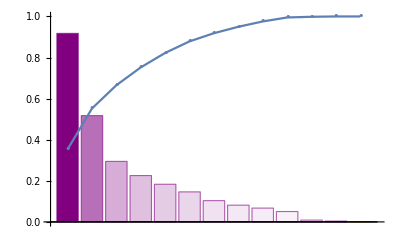
I replicated Aouidate, et al’s Principal Component Analysis. Here is a bar chart of 1/5 the variance of each component overlaid with a ListLinePlot of the accumulated variance:
-Graphics-

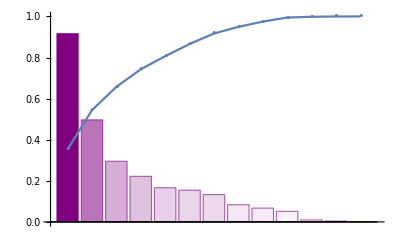
And here is the same analysis with the normalized data:
-Graphics-

Here is the correlation matrix of Aouidate’s data:

(1. | -0.445075 | -0.264673 | 0.37217 | -0.577815 | -0.333557 | -0.259118 | -0.352955 | 0.196377 | 0.342209 | 0.0539286 | -0.0293615 | 0.199581 | 0.531941
-0.445075 | 1. | -0.0838851 | 0.271229 | 0.258482 | 0.606635 | -0.294584 | 0.33373 | -0.251888 | -0.526888 | -0.351307 | -0.194399 | -0.74975 | -0.202031
-0.264673 | -0.0838851 | 1. | -0.555216 | 0.460072 | -0.00474525 | 0.0570004 | 0.0222463 | 0.0328363 | -0.279507 | 0.0631735 | -0.0262394 | 0.0985546 | -0.246192
0.37217 | 0.271229 | -0.555216 | 1. | -0.633469 | 0.25258 | -0.269334 | -0.0991034 | -0.208526 | 0.0429598 | -0.150405 | -0.0484502 | -0.239614 | 0.395812
-0.577815 | 0.258482 | 0.460072 | -0.633469 | 1. | 0.588676 | -0.120574 | 0.605684 | -0.14666 | -0.430435 | -0.396205 | -0.383033 | -0.126844 | -0.509443
-0.333557 | 0.606635 | -0.00474525 | 0.25258 | 0.588676 | 1. | -0.432335 | 0.653866 | -0.401401 | -0.493919 | -0.652339 | -0.52948 | -0.408954 | -0.223622
-0.259118 | -0.294584 | 0.0570004 | -0.269334 | -0.120574 | -0.432335 | 1. | -0.307771 | 0.0261029 | 0.313594 | 0.250516 | 0.201145 | 0.0827052 | -0.11172
-0.352955 | 0.33373 | 0.0222463 | -0.0991034 | 0.605684 | 0.653866 | -0.307771 | 1. | -0.167066 | -0.325735 | -0.370674 | -0.309641 | -0.110675 | -0.392581
0.196377 | -0.251888 | 0.0328363 | -0.208526 | -0.14666 | -0.401401 | 0.0261029 | -0.167066 | 1. | 0.0568898 | 0.467254 | 0.426957 | 0.334716 | 0.0524229
0.342209 | -0.526888 | -0.279507 | 0.0429598 | -0.430435 | -0.493919 | 0.313594 | -0.325735 | 0.0568898 | 1. | 0.198254 | 0.164145 | 0.290585 | 0.323211
0.0539286 | -0.351307 | 0.0631735 | -0.150405 | -0.396205 | -0.652339 | 0.250516 | -0.370674 | 0.467254 | 0.198254 | 1. | 0.951168 | 0.627186 | 0.176771
-0.0293615 | -0.194399 | -0.0262394 | -0.0484502 | -0.383033 | -0.52948 | 0.201145 | -0.309641 | 0.426957 | 0.164145 | 0.951168 | 1. | 0.578043 | 0.116499
0.199581 | -0.74975 | 0.0985546 | -0.239614 | -0.126844 | -0.408954 | 0.0827052 | -0.110675 | 0.334716 | 0.290585 | 0.627186 | 0.578043 | 1. | 0.0434568
0.531941 | -0.202031 | -0.246192 | 0.395812 | -0.509443 | -0.223622 | -0.11172 | -0.392581 | 0.0524229 | 0.323211 | 0.176771 | 0.116499 | 0.0434568 | 1.)

The column indices in the above are:

```mathematica
{"logMU","ET","IP","EHOMO","η","ELUMO","DM","Qp","Qmin","MW","n","γ","D","logP"}
```

Functions to Compare Linear or Non-linear Models:

In collaboration with Kyle Keane, I developed a function to take a design matrix with n columns and compare all nCr combinations of r columns and find the model with the best R^2 value:

```mathematica
allRSquared=MapIndexed[
Function[
{parameters,index},
regressThese=Part[reformatted12,All,parameters];
First@index->LinearModelFit[regressThese,Table[x[i],{i,1,5}],Table[x[i],{i,1,5}]]["RSquared"]
],
whichParameters2
];
```

The notebook in which this has actually been run can be found in my Github at: https://github.com/madsutherland/Project/blob/master/Molecular%20Structures%20Real/Final%20Aouidate%20Analysis%20Notebook.nb

I also made a non-linear version in the same notebook. Here’s what it looks like:

```mathematica
allRSquaredNonlinear=MapIndexed[
Function[
{parameters,index},
regressThese=Part[reformatted12,All,parameters];
First@index->NonlinearModelFit[regressThese,a+b x1+c x2+d x3+e x4+f x5+l x1^2+m x2^2+n x3^2+o x4^2+p x5^2,{a,b,c,d,e,f,l,m,n,o,p},
{x1,x2,x3,x4,x5}]["RSquared"]
],
whichParameters2
];
```

### Results:

For a chemist or biologist analyzing data, Mathematica has a lot to offer:
• Built-in functions are often listable and can deal with negative numbers as input
• Ability to view data in matrix form and overlay plots
• Ease of writing new functions
I was able to replicate Aouidate, et al’s Principal Component Analysis and correlation matrix, and achieve similar results before and after normalizing the data.
I applied the function I wrote to compare linear models by R^2 value to the normalized and non-normalized data. Here are the column numbers of the five best models:
	Non-Normalized:
	(1 | 4 | 6 | 10 | 12 | -1
1 | 4 | 6 | 8 | 10 | -1
1 | 4 | 6 | 11 | 12 | -1
1 | 4 | 6 | 8 | 11 | -1
1 | 4 | 6 | 10 | 11 | -1)
	Normalized:
	(1 | 4 | 6 | 10 | 12 | -1
1 | 4 | 6 | 11 | 12 | -1
1 | 4 | 6 | 8 | 10 | -1
1 | 3 | 5 | 6 | 11 | -1
1 | 4 | 6 | 10 | 11 | -1)

These represent the variables: 1 -> total energy, 3 -> energy of the Highest Occupied Molecular Orbital (HOMO), 4 -> absolute hardness (the inverse of softness/polarizability), 5 -> energy of the Lowest Unoccupied Molecular Orbital (LUMO), 6->dipole moment calculated by DFT, 8->most negative net atomic charge, 10 -> surface tension, 11-> density, 12-> logP (log octanol/water partition coefficient). Descriptors 1, 3, 4, 5, 6 and 8 were from DFT while 10, 11, and 12 were physicochemical descriptors. Although the data going into this analysis had 8 DFT descriptors and 5 physicochemical, many of the top models had four DFT descriptors and one physicochemical. Thus, the outcome was consistent with the hypothesis that DFT descriptors provide value to QSAR models. I also independently generated a more traditional set of physicochemical descriptors and applied this analysis to rigorously balanced data sets; the top models still made heavy use of DFT. Interestingly, I could not get a good fit for the data without including the dipole moment values calculated by DFT.

## Manipulation of Structures, 3D Images:

I collaborated with Robert Nachbar to develop a toolkit to make and export 3D images. Below I will show the functions and explain what they do, but I’ll refer the reader to this Github address for my actual implementation: https://github.com/madsutherland/Project/blob/master/Molecular%20Structures%20Real/output%20test.nb

From Bob’s package which I used to generate atomic coordinates:

MakeZmatrixMolecule: 
-Graphics-

ShowMolecule:

ShowMolecule[mol] returns a Graphics3D rendering of the molecule mol.

Example:

```mathematica
mol[43]=MakeZmatrixMolecule[zmat43,params,"RingBonds"->{{6,1}->"𝒹"}]
```

<|Atoms→{C,C,C,C,C,C,C,C,N,O,C,O,C,O,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H,H},Bonds→{{{2,1},𝓈},{{3,2},𝒹},{{4,3},𝓈},{{5,4},𝒹},{{6,5},𝓈},{{7,1},𝓈},{{8,7},𝓈},{{9,8},𝓈},{{10,3},𝓈},{{11,10},𝓈},{{12,4},𝓈},{{13,12},𝓈},{{14,5},𝓈},{{15,14},𝓈},{{6,1},𝒹},{{2,16},𝓈},{{6,17},𝓈},{{7,18},𝓈},{{7,19},𝓈},{{8,20},𝓈},{{8,21},𝓈},{{9,22},𝓈},{{9,23},𝓈},{{11,24},𝓈},{{11,25},𝓈},{{11,26},𝓈},{{13,27},𝓈},{{13,28},𝓈},{{13,29},𝓈},{{15,30},𝓈},{{15,31},𝓈},{{15,32},𝓈}},AtomCoordinates→{{0.,0.,0.},{-1.333,0.,0.},{-1.9995,1.15441,0.},{-1.333,2.30882,0.},{1.33227×10^-15,2.30882,0.},{0.6665,1.15441,0.},{0.763,-1.32155,-1.61844×10^-16},{1.01733,-1.76207,1.43873},{1.73903,-3.01208,1.2903},{-3.3125,1.15441,-1.39254×10^-16},{-3.64593,1.15441,-1.37824},{-1.9895,3.44592,-1.39254×10^-16},{-2.15622,3.73468,1.37824},{0.6565,3.44592,-1.39254×10^-16},{0.823216,3.73468,-1.37824},{-1.8855,-0.956958,0.},{1.7715,1.15441,0.},{1.72852,-1.18943,-0.520902},{0.165814,-2.09166,-0.520902},{0.065394,-1.91772,1.97781},{1.6281,-1.01549,1.97781},{1.92319,-3.33107,2.3321},{2.69097,-2.85643,0.751217},{-4.75093,1.15441,-1.37824},{-3.2514,0.252183,-1.8796},{-3.2514,2.05664,-1.8796},{-2.70872,4.69163,1.37824},{-1.1776,3.84412,1.8796},{-2.74031,2.94189,1.8796},{1.37572,4.69163,-1.37824},{-0.155401,3.84412,-1.8796},{1.40731,2.94189,-1.8796}}|>

```mathematica
ShowMolecule[mol[43],"ShowHydrogens"->True,"ShowLabels"->True]
```

-Graphics3D-

We created this function to associate elements with their van der Waals radii:

```mathematica
vdwRadii=Rule@@@(Outer[ElementData[Entity["Element",#1],#2]&,{"Hydrogen","Carbon","Nitrogen","Oxygen","Sulfur"},{"Abbreviation","VanDerWaalsRadius"}]/.{a_String,r_}:>{a,QuantityMagnitude@UnitConvert[r,"Angstroms"]})//Association
```

This one imports Cartesian atomic coordinates:

```mathematica
coords=molecules["mol43assoc","AtomCoordinates"];
```

This adds space around the atomic coordinates for the clouds of electrons:

```mathematica
minMax=(resolution{Floor[(1/resolution)#1],Ceiling[(1/resolution)#2]}&)@@@({-2,2}+#&)/@MinMax/@Transpose@coords
```

This makes a 3D grid with vector coordinates at each point:

```mathematica
grid=With[{iter=Sequence@@MapThread[Prepend,{Append[#,resolution]&/@minMax,{x,y,z}}]},Table[{x,y,z},iter]];
Dimensions@% (*Makes a grid with vector coordinates at each point, shows dimensions*)
```

This is a quick and dirty test for whether a point is close enough to an atom to be considered:

```mathematica
boxedQ[grid_,atom_,r_]:=And@@MapThread[Hold[#1-r≤#2≤#1+r]&,{atom,grid}]//ReleaseHold
```

This maps over each point in the space the atomic index of any atom whose radius the point is within:

```mathematica
closestAtom[grid_]:=MapThread[Module[{d2},If[boxedQ[grid,#1,#2]&&With[{d=grid-#1},(d2=d.d)≤#3],{d2,#4},Nothing]]&,{coords,radii,radii^2,Range[nAtoms]}]//Sort//First[#,0]&
```

And this converts the image to a grid of electronegativities:

```mathematica
electronegativityGrid256=Map[atomElectronegativities256,gridAtoms,{3}];
```

The result is an image3D with electronegativities of the atoms at each point. It looks pretty neat! I’m just putting a screenshot since the file is large.

For the Aouidate data set, our 3D conformations were based on some chemical assumptions rather than hard data, and these images wouldn’t provide much extra insight. But in the future, I can use this framework when I’m analyzing 3D electron density grids.

## Machine Learning and Neural Nets for Phenotypic Prediction:

For this part of my project, I would refer the reader to the following Github link: https://github.com/madsutherland/Project/blob/master/Molecular%20Structures%20Real/DNN%20Aouidate%20original%20data.nb 
In collaboration with Markus van Almsick, I tested the ability of Predict[] and a simple neural net to predict logMUs, to see if those algorithms faired better than simple backwards regression. As input I also included a vectorized rendering of the molecular structures. 
In actuality, the resulting models had a similar Mean Standard Error to Aouidate, et al’s Multiple Non-Linear Regression (MNLR). By my calculation, the results are as follows:
Mean Squared Residual from Aouidate’s MNLR: 0.136
From Predict[]: 0.112
From a Neural Net: 0.232

## Conclusions:

The loss function in the neural net did not converge.  I believe that this data set was not chemically very rich, and that the response variable was inherently hard to predict because it was a phenotypic outcome as opposed to a target engagement outcome - in other words, it was a function of multiple molecular interactions rather than just one.  It is possible that Predict[] and/or neural nets will aid the analysis of richer QSAR data sets in the future. As always, computation and experimentation are like the shoes on your feet: you get farther with both than just one or the other.

## Future Directions:

• Build a function to compare models based on Mean Standard Error between predicted and output values and other statistics besides R^2.
• Generate more chemically diverse data sets, try feeding them into a neural net 
• Map calculated electron density data over 3D chemical structure grid
• Test ability of neural net to predict target engagement of drug structures from rich, structurally diverse SAR data.

## Project Summary:

My project will test the ability of a neural net to perform a Quantitative Structure-Activity Relationship (QSAR) study on a series of phenylalkylamine drugs.
In QSAR, data on the structure and properties of structurally related compounds with known biochemical activity are used to build a model to predict the activity of additional compounds in that series. Traditional descriptors have included the octanol/water partition coefficient LogP, molecular weight and Total Polar Surface Area (TPSA) and two-dimensional structure. In the past couple years, there has been increasing interest in use of three-dimensional, energetically optimized structure and quantum chemical descriptors from Density Functional Theory (DFT) calculations. Anecdotally, such descriptors have led to models with good fit.
Here, we are working with phenylalkylamines, whose mechanism of action and binding mode is unknown. So, we will first create z-matrices for the structures of the compound with all the possible combinations of cis and trans conformations of each substituent on the ring with respect to the alkylamine substituent. We will align all the conformations of the compounds with respect to a reference, and see if one conformation gives particularly good agreement across this series of active drugs. If so, that conformation will be used for all the compounds in the series.
Then, we will convert the z-matrices into 3D image matrices via the hard sphere model, and assign voxels corresponding to atomic number at the appropriate atomic radius around each atom. 
A training set of those 3D images and the biochemical activities of their respective compounds will then be fed into Predict[], since biochemical activity is a continuous variable (in this case, logMU, the log of effective doses of the compound in question and mescaline). 
We will analyze the resulting model with respect to its ability to predict the biochemical activities of the remaining test set of compounds. 
We hope to create a generalizeable framework that can be applied to additional data set.  In the future, we could perform a meta-analysis to see what types of variables/descriptors make the most robust QSAR models in the context of machine learning.

## References:

1	Aouidate, et al. "Combining DFT and QSAR studies for predicting psychotomimetic of substituted phenethylamines using statistical methods." Journal of Taibah University for Science 10 (2016): 787-796.